# It's NanoTech, Do you like it Jarvis?

-Subhendu Pandit, U of I

## Introduction

```mathematica
Quit
```

The hope of making a wonder material to selectivity detect and destroy cancer cells still remains the holy grail of cancer diagnosis and therapy. Nano-materials, the most fashionable materials of modern times with highly unusual properties, promised a lot to be that ‘wonder material.’ However, is it holding up to its promise? We are about to have a closer look at it in a data-driven approach. How do we go about it?
How about we pretend ourselves to be the legendary Tony Stark and ask Tony’s AI interface Jarvis to give us an analysis? In ‘Stark-swag’ lets ask, “It’s NanoTech, do you like it Jarvis?” and Jarvis replies, “Working on it, Sir!”

```mathematica
ironmanimage=WebImageSearch["Ironman and JARVIS",Method->"Bing", MaxItems->3];
Manipulate[ironmanimage[[ChooseYourFavImage]][[1]],{{ChooseYourFavImage,2,"Choose your favourite Image"},Range[3]},SaveDefinitions->True]
```

To answer the question, Jarvis enquires the Cancer Nano-medicine Repository (CNR). CNR is an online open-access resource to track and organize data on nanoparticle delivery efficiency to solid tumors. Monitoring the delivery efficiency of nanomaterials to solid cancer tumors is of prime importance. No matter how wonderful your nanotech system is, if it does not reach the tumor, it is not likely to work (Nature Reviews Materials 2016, 1, 16014.) CNR keeps an organized dataset of physicochemical properties of nanoparticles (such as hydrodynamic diameter, zeta potential, particle shape, etc.) along with their delivery efficiency to solid tumors. Jarvis fetches the dataset, and decided mainly the following two questions:

#### Are physicochemical properties of nanoparticle correlated with their delivery efficiency?

JARVIS intend to present the dataset in an interactive fashion and let Mr. Stark look for any correlation of any property of nanomaterials with their delivery efficiency.

#### Are certain particles more efficient than others and can we train a Machine Learning model to predict that?

JARVIS also decided to try to ‘learn’ and classify the data set to identify nanoparticles with higher delivery efficiency. A predictive function that takes the physicochemical properties as input and  predicts the delivery efficiency would be wonderful. Any insight form JARVIS’s learning might provide a data-driven approach to reshape future efforts of developing new cancer nanotech drug with higher delivery efficiency.

## Cancer Nano-medicine Repository (CNR)

CNR keeps are nicely curated data set for all the nanomaterials based system published in last 10 years. The dataset includes relevant physio-chemical properties of the nanomaterials along with their delivery efficiency to solid tumors.

Importing the CNR data:

```mathematica
nanoData=SemanticImport["http://inbs.med.utoronto.ca/wp-content/uploads/statsCNR/Data/CNR_data.csv"];
nanoData=nanoData/.""->"N/A"
```

Dataset[<>]

## Visualization

### Quick Exploratory Visualization of numeric portion of the dataset

‘Here is a quick visualization, Sir.’ says JARVIS.

```mathematica
Manipulate[
ListPlot[nanoData[All,{x,"Delivery Efficiency (%ID)"}],PlotRange->range, AxesLabel->{x,"Delivery Efficiency (%ID)"},BaseStyle->{FontWeight->"Bold",FontSize->12},ImageSize->Large],
{x,{"Particle Diameter (nm)","Zeta Potential (mV)","Publication Year"}}, {range,{Full,Automatic}},SaveDefinitions->True]
```

‘That is not very helpful Jarvis. Give me visual of the graph with the data points in differnt colors according to diffenent physciochemical properties.’
‘working on it, Sir.’

### Colorizing the data points according to different properties

```mathematica
coloredbyproperty=
Manipulate[
elements=DeleteDuplicates[Normal[nanoData2[All,colorby]]];(*extracting unique elements from colorby column*)
colormap=ColorData["BrightBands",#]&/@Table[i,{i,0,1,1/(Length@elements-1)}];(*creating no of unique element colors form a colormap*)
assoc=AssociationThread[elements->colormap];(*associating each unique element in colorby with a generated color*)
color=Normal[nanoData⟦All,colorby⟧]/.assoc;(*Replacing those unique keywords in nanoData with the color*)
temp=Normal[nanoData⟦All,{x,"Delivery Efficiency (%ID)"}⟧];(*this is generating dataset for intended xy plot*)
dat=Cases[Transpose[{color,temp}],{#,_}]⟦All,2⟧&/@colormap;(*this is separating the elements form temp according to its colortag*)
finalPlot=plotType[dat,PlotLegends->Placed[elements,Top],PlotStyle->colormap,PlotRange->range,AxesLabel->{x,"Delivery Efficiency (%ID)"},BaseStyle->{FontWeight->"Bold",FontSize->font},ImageSize->sizeofGraph];(*Plotting the dataset in associated color*)

If[export,Export[NotebookDirectory[]<>"/"<>"Graph_"<>x<>"_"<>colorby<>"_export.pdf",finalPlot];export=False];(*Defining the export name*)

finalPlot,
(*Here goes all the manipulate buttons*)
{{x,"Particle Diameter (nm)","X-axis"},{"Particle Diameter (nm)","Zeta Potential (mV)","Publication Year"}},
{{colorby,"Targeting Strategy","Color Points by"},{"Particle Type","Inorganic Material","Organic Material","Targeting Strategy","Particle Shape","Tumour Model","Cancer Type"}},
{{plotType,ListLogPlot,"Plot Style"},{ListPlot, ListLogPlot}},
{{range,Full, "Range"},{Full,Automatic}},
{{sizeofGraph,"Large","Size of the Graph"},{"Large","Full"}},
{{font,12,"Font Size"},{12,14,16,18,20,22,24,26,28,30}},

Button["Export this Graph as PDF to Notebook Folder", export=True],
SaveDefinitions->True];
```

```mathematica
coloredbyproperty
```

‘Perfect! Thanks Jarvis.’
The data points look very random when delivery efficiency is plotted against the particle diameter, zeta or publication year. The classification by different other properties does not provide any obvious clustering either. However, one this is pretty consistent over all the data points, that is the delivery efficiency is very low for all the nanoparticle based systems which seems to be ~1% looking at the visualization. The only clear conclusion that could be drawn might be Inorganic Gold Nanoparticles delivers well  for skin cancer models and a few other very niche observations. However, overall no obvious trend in the data could be observed to draw strong correlation between any of the physio-chemical properties and delivery efficiency.
‘Jarvis, what do you think of the data? Can you predict the delivery efficiency from the given parameters?’
‘On it Sir!’ **Initializing the Artificial Intelligence analysis**

## Machine Learning

### Prediction with original data

Reimporting and splitting the data:

```mathematica
nanoData=Import["http://inbs.med.utoronto.ca/wp-content/uploads/statsCNR/Data/CNR_data.csv"];
Length@nanoData
```

239

```mathematica
titles=nanoData[[1]]
```

{Particle Type,Inorganic Material,Organic Material,Targeting Strategy,Particle Diameter (nm),Zeta Potential (mV),Particle Shape,Tumour Model,Cancer Type,Delivery Efficiency (%ID),Publication Year}

```mathematica
data=nanoData[[2;;239]];
data2=Thread[data[[All,1;;9]]->data[[All,10]]];
Length@data2
```

238

```mathematica
{trainingdata,testdata}=TakeDrop[RandomSample[data2],200];(*randomly selecting 200 data points for training and rest for test*)
trainingdata//Length
testdata//Length
```

200

38

Performing regression analysis on a randomly spitted data of 200 training cases and 38 test cases:

```mathematica
pf=Predict[trainingdata]
```

PredictorFunction[…]

```mathematica
PredictorMeasurements[pf,testdata,{"StandardDeviation","LogLikelihood"}]
```

{1.05693,-77.6127}

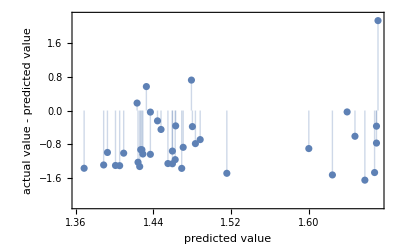
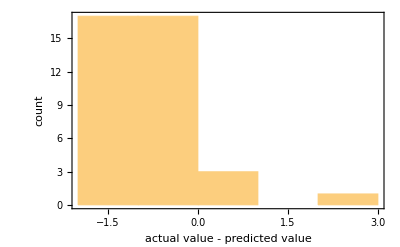
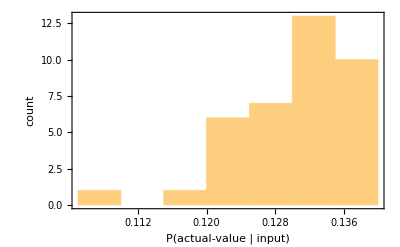

```mathematica
PredictorMeasurements[pf,testdata,{"ResidualPlot","ResidualHistogram","ProbabilityDensityHistogram"}]
```

```mathematica
PredictorMeasurements[pf,testdata,"WorstPredictedExamples"]
```

{{Inorganic,Gold,,Passive,166,-6,Spherical,Xenograft Orthotopic,Skin}→3.8,{Inorganic,Gold,,Passive,22,0,Spherical,Xenograft Orthotopic,Skin}→0.01,{Inorganic,Silica,,Passive,7,0,Spherical,Xenograft Orthotopic,Skin}→0.1,{Inorganic,Gold,,Passive,60,-11,Spherical,Xenograft Heterotopic,Prostate}→0.03,{Inorganic,Silica,,Active,7,-3,Spherical,Xenograft Orthotopic,Skin}→0.2,{Organic,,Hydrogels,Passive,50,-45,Spherical,Allograft Heterotopic,Liver}→0.1,{Organic,,Polymeric,Passive,268,-37,Rod,Xenograft Heterotopic,Ovary}→0.002,{Organic,,Liposomes,Passive,51,-4,Spherical,Xenograft Heterotopic,Unknown}→0.1,{Organic,,Hydrogels,Passive,201,-14,Spherical,Allograft Heterotopic,Breast}→0.1,{Organic,,Other,Passive,86,71,Spherical,Xenograft Heterotopic,Lung}→0.1}

The predictor function does not predict very well which is clearly visualized by the predictor measurement graphs.

### Prediction with modified parameters

The first three column gives redundant information. If there is only organic material present, particle type is organic. It is similar for inorganic and if both are present it is hybrid. So, I decided to combine these three into one column ‘Materials’. Let us see if this improves the prediction efficiency of the regression analysis.

```mathematica
Quit
```

```mathematica
nanoData=Import["http://inbs.med.utoronto.ca/wp-content/uploads/statsCNR/Data/CNR_data.csv"];
newcolumn=(nanoData[[#,2]]~~" "~~nanoData[[#,3]])&/@Range@Length[nanoData];(*Joining the string to a single column 'Materials*)
newcolumn=ReplacePart[newcolumn, 1->"Materials"]
```

{Materials,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Gold ,Other ,Iron Oxide ,Iron Oxide ,Iron Oxide ,Iron Oxide ,Iron Oxide ,Iron Oxide ,Iron Oxide ,Iron Oxide ,Silica ,Silica ,Silica ,Silica ,Silica ,Silica ,Silica ,Silica ,Silica ,Silica ,Silica ,Silica ,Silica ,Other ,Other ,Other ,Other ,Other ,Other ,Other ,Other ,Other ,Other ,Other ,Other ,Other ,Other ,Quantum Dots ,Quantum Dots ,Quantum Dots ,Quantum Dots ,Quantum Dots ,Quantum Dots Liposomes,Quantum Dots Liposomes,Quantum Dots Liposomes,Iron Oxide Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Polymeric, Other, Other, Other, Other, Other, Other, Other, Other, Other, Other, Other, Other, Other, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Liposomes, Hydrogels, Hydrogels, Hydrogels, Hydrogels, Hydrogels, Hydrogels, Hydrogels, Hydrogels, Hydrogels, Hydrogels, Hydrogels, Hydrogels, Hydrogels, Hydrogels, Hydrogels, Hydrogels, Hydrogels, Hydrogels, Dendrimers, Dendrimers, Dendrimers, Dendrimers, Dendrimers, Dendrimers, Dendrimers,Gold Dendrimers,Gold Dendrimers,Gold Dendrimers,Gold Dendrimers,Gold Dendrimers, Other, Other, Other, Other, Other, Other, Other, Other, Other, Other,Gold ,Gold ,Gold ,Gold ,Gold ,Gold }

200

38

PredictorFunction[…]

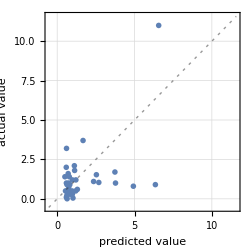
Predictor Measurements
Number of test examples | 38
Standard deviation | 1.66 ± 0.31
Standard deviation baseline | 1.78 ± 0.77
Mean cross entropy | 2.02 ± 0.32
Single evaluation time | 11.4 ms/example
Batch evaluation speed | 970. examples/s
-Graphics- |

```mathematica
x=Normal[nanoData[[All,4;;10]]];
whatever=Transpose[Insert[Transpose[x],newcolumn,1]];
data=whatever[[2;;239]];
data2=Thread[data[[All,1;;7]]->data[[All,8]]];
{trainingdata,testdata}=TakeDrop[RandomSample[data2],200];
trainingdata//Length(*These are just to make sure we have splitted the data in an intended way*)
testdata //Length
pf=Predict[trainingdata,Method->"GradientBoostedTrees"]
PredictorMeasurements[pf,testdata,"Report"]
```

```mathematica
PredictorMeasurements[pf,testdata,{"StandardDeviation","LogLikelihood"}]
```

{1.65973,-76.7739}

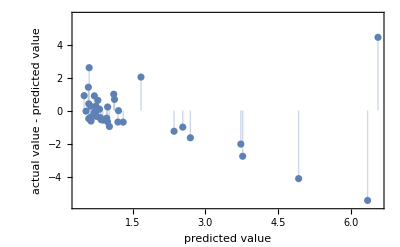
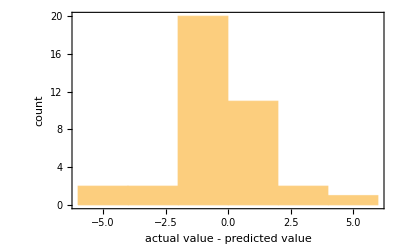
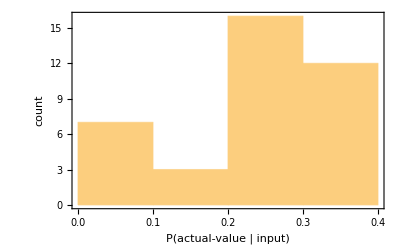

```mathematica
PredictorMeasurements[pf,testdata,{"ResidualPlot","ResidualHistogram","ProbabilityDensityHistogram"}]
```

‘Good job Jarvis! That looks much better!’

### Clustering

Jarvis also thinks unsupervised learning can be employed to classify the points to gain some possible insight into the dataset.

```mathematica
classifierKernels=ClusterClassify[whatever]
```

ClassifierFunction[…]

```mathematica
labelsKernels = classifierKernels[whatever ]
```

{1,2,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,5,4,5,4,1,1,1,1,3,1,1,1,1,1,1,1,1,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,2,5,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Dataset/@(Pick[whatever, labelsKernels, #]&/@Range@5)(*separating the dataset into 5 predicted classes to see the elements individually*)
```

{Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>],Dataset[<>]}

#### Visualization:

```mathematica
ListPointPlot3D[Pick[DimensionReduce[whatever, 3], labelsKernels, #]&/@Range@5,PlotStyle-> {Blue, Green, Red,Black, Magenta},ImageSize->500,PlotLabel->Style[Framed["Feature Space Plot"],16,Bold,Background->Lighter[Yellow]],AxesStyle->Thick,BoxStyle->Thick](*Plotting the groups in a 3D spcae for better visulization*)
```

-Graphics3D-

As it is frequently the case with machine learning algorithms, it is very difficult to understand what property is leading to these five clusters.

### Good or Bad

To further simplify the problem for a better prediction efficiency using Machine Learning, Jarvis designates all the nanomaterials with >1% delivery efficiency to be ‘Good’ and the others to be ‘Bad’. Then he tries to look at the prediction efficiency form the given physio-chemical parameters.

ClassifierFunction[…]

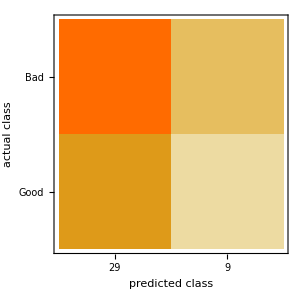
Classifier Measurements
Number of test examples | 38
Accuracy | (61.8.) %
Accuracy baseline | (68.8.) %
Geometric mean of probabilities | 0.517 ± 0.042
Mean cross entropy | 0.659 ± 0.081
Single evaluation time | 3.97 ms/example
Batch evaluation speed | 6.06 examples/ms
Rejection rate | 0 %
-Graphics- |

```mathematica
nanoData=Import["http://inbs.med.utoronto.ca/wp-content/uploads/statsCNR/Data/CNR_data.csv"];
newcolumn=(nanoData[[#,2]]~~" "~~nanoData[[#,3]])&/@Range@Length[nanoData];(*modifying the datatset to add the 'Materials' column collating the previous two column data*)
newcolumn=ReplacePart[newcolumn, 1->"Materials"];
x=Normal[nanoData[[All,4;;9]]];
whatever=Transpose[Insert[Transpose[x],newcolumn,1]];
data=whatever[[2;;239]];
cutoff=1;(*Setting the Cutoff for 'Good' and 'Bad'*)
goodbad=nanoData[[All,10]][[2;;]]/.x_/;x>cutoff->"Good"/.x_/;x≠"Good"->"Bad";(*Asoociating the data to the descriptor*)
data2=Thread[data->goodbad];
{trainingdata,testdata}=TakeDrop[RandomSample[data2],200];
cf=Classify[trainingdata, PerformanceGoal->"Quality"]
ClassifierMeasurements[cf,testdata,"Report"]
```

‘Hmm, that is better! The algorithms could correctly predict a nanomaterial to have good or bad delivery efficiency with 61% accuracy!’
A little red flag: As we are randomly splitting the data, the confusion matrix changes every time we run the code and the same concern remains for the following analysis section too.

#### Hyper-parameter Tuning: Method

Jarvis delves into hyper-parameter tuning to make the methods even better for prediction.

```mathematica
AssociationMap[ ClassifierMeasurements[
Classify[trainingdata,Method->#],testdata, "Accuracy"]&,{"RandomForest", "NaiveBayes", "SupportVectorMachine", "NearestNeighbors","LogisticRegression","GradientBoostedTrees","DecisionTree"}]
```

<|RandomForest→0.605263,NaiveBayes→0.552632,SupportVectorMachine→0.605263,NearestNeighbors→0.5,LogisticRegression→0.631579,GradientBoostedTrees→0.631579,DecisionTree→0.526316|>

#### Hyper-parameter Tuning: BoostingMethod

```mathematica
AssociationMap[ ClassifierMeasurements[
Classify[trainingdata,Method->{"GradientBoostedTrees","BoostingMethod"->#}],testdata, "Accuracy"]&,{"Gradient", "GradientOneSideSampling", "DART"}]
```

<|Gradient→0.631579,GradientOneSideSampling→0.684211,DART→0.631579|>

#### Hyper-parameter Tuning: LeafSize

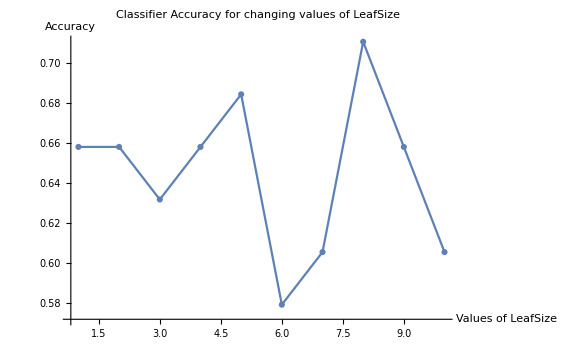

```mathematica
cmaccuracy={#,ClassifierMeasurements[Classify[trainingdata, RandomSeeding -> 1234,PerformanceGoal->"Quality",Method->{"GradientBoostedTrees","BoostingMethod"->"GradientOneSideSampling","LeafSize"-> #}], testdata, "Accuracy"]}&/@ Range[10];
ListLinePlot[cmaccuracy, PlotMarkers->Automatic,PlotRange -> All, PlotLabel -> Style["Classifier Accuracy for changing values of LeafSize", "Subsubsection",Darker[Red]], AxesLabel -> {Style["Values of LeafSize",18], Style["Accuracy",18]}, ImageSize -> Large]
```

#### Hyper-parameter Tuning: L1Regularization

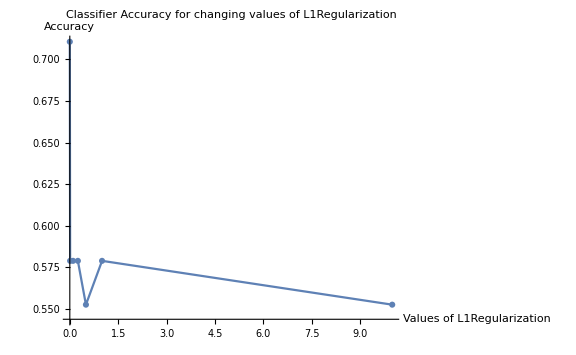

```mathematica
cmaccuracy={#,ClassifierMeasurements[Classify[trainingdata, RandomSeeding -> 1234,PerformanceGoal->"Quality",Method->{"GradientBoostedTrees","BoostingMethod"->"GradientOneSideSampling","LeafSize"-> 8,"L1Regularization"-> #}], testdata, "Accuracy"]}&/@ {0.0,0.01,0.1,0.25,0.5,1.0,10};
ListLinePlot[cmaccuracy, PlotMarkers->Automatic,PlotRange -> All, PlotLabel -> Style["Classifier Accuracy for changing values of L1Regularization", "Subsubsection",Darker[Red]], AxesLabel -> {Style["Values of L1Regularization",18], Style["Accuracy",18]}, ImageSize -> Large]
```

#### Hyper-parameter Tuning: L2Regularization

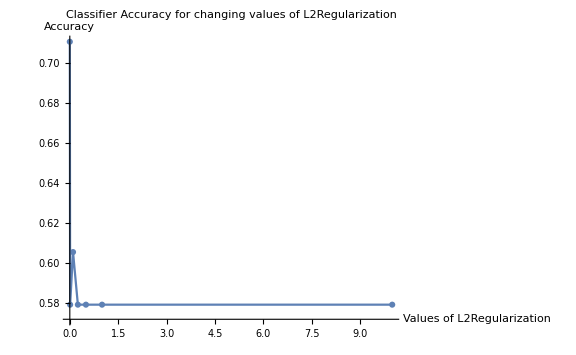

```mathematica
cmaccuracy={#,ClassifierMeasurements[Classify[trainingdata, RandomSeeding -> 1234,PerformanceGoal->"Quality",Method->{"GradientBoostedTrees","BoostingMethod"->"GradientOneSideSampling","LeafSize"-> 8,"L2Regularization"-> #}], testdata, "Accuracy"]}&/@ {0.0,0.01,0.1,0.25,0.5,1.0,10};
ListLinePlot[cmaccuracy, PlotMarkers->Automatic,PlotRange -> All, PlotLabel -> Style["Classifier Accuracy for changing values of L2Regularization", "Subsubsection",Darker[Red]], AxesLabel -> {Style["Values of L2Regularization",18], Style["Accuracy",18]}, ImageSize -> Large]
```

#### Final Classifier

So, from the hyperparameter tuning Jarvis could figure out the optimal parameters to be GradientBoostedTrees with BoostingMethod→GradientOneSideSampling and LeafSize→ 8.

ClassifierFunction[…]

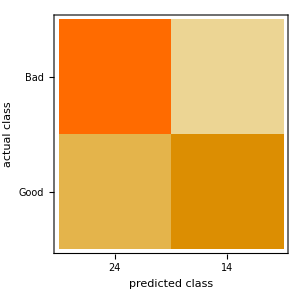
Classifier Measurements
Number of test examples | 38
Accuracy | (71.7.) %
Accuracy baseline | (55.8.) %
Geometric mean of probabilities | 0.548 ± 0.044
Mean cross entropy | 0.602 ± 0.081
Single evaluation time | 5.24 ms/example
Batch evaluation speed | 6.25 examples/ms
Rejection rate | 0 %
-Graphics- |

```mathematica
cf=Classify[trainingdata, RandomSeeding -> 1234,PerformanceGoal->"Quality",Method->{"GradientBoostedTrees","BoostingMethod"->"GradientOneSideSampling","LeafSize"-> 8}]
ClassifierMeasurements[cf,testdata,"Report"]
```

"Sir, I could formulate a algorithm to predict the delivery efficiency with just two descriptors with 71% accuracy."
“Good job! Jarvis!”
Note: Again the accuracy % and hyper tuning parameters may change every time we are randomly splitting the data.

## Conclusion

Our little exploration with Jarvis into the CNR data could bring out the following features of the dataset:

The visualization of original data in classic graphical form does not give much insight. It only tells us that irrespective of physio-chemical properties, overall nanoparticle delivery efficiency is low to solid tumors. So, there is not obvious correlation between any single physio-chemical properties of nanoparticles with its delivery efficiency. However, a interactive way of plotting the data in all possible ways with different color codes has been achieved using the Wolfram language.

Regression Analysis could predict the delivery efficiency with standard deviation of 1.66 with some modified concise data.

Unsupervised Learning predicted five classes which Jarvis is unsure about what it represents in terms of Cancer Nano-medicine.

Supervised learning with some hyperparameter tuning could predict if the delivery efficiency would be above 1% or below with a 71% accuracy.

The last three conclusions listed above could change every time we randomly split the data into training and the test set. However, every time Jarvis analyzed it, he could get to a model with some hyperparameter tuning to have prediction efficiency ~60-75%. So, using the supervised learning Jarvis could come up with a predictive model which can predict if the delivery efficiency of a nanomaterial could be >1% or not form its physio-chemical properties with 60-80% efficiency.

#### Future Work

There is a lot more to explore on this dataset to come up with a reliable machine learning model to predict delivery efficiency of the nanomaterials-based cancer drugs in silico. Some of the future further exploration would include:

Understanding how splitting the data is affecting the results to get to a robust, reliable and reproducible model for the predictions.

Interpret the unsupervised learning results to understand how the clustering happening to gain insight into possible physio-chemical parameter combinations affecting the delivery efficiency of the nanoparticles.

We could think about some other ways of splitting the data but that would likely introduce over-fitting problem. We can take first 9 years of data to train the model and try to predict the performance of the nano-materials that came out in last one year.